```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/critical_region/Tc/LPA/buffer

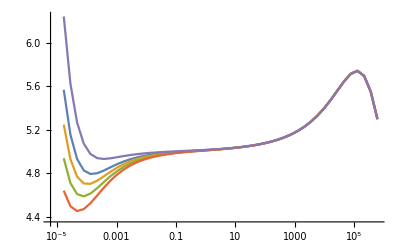

```mathematica
fpi=Flatten[Import["./T132p15097/fpi.dat"]];
cl=Flatten[Import["./T132p15097/c.dat"]];
csdata=Transpose[{Log[cl],Log[fpi]}];
cslogdata=Transpose[{Log[cl*197.33^3],Log[fpi]}];
a1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-1}];
b1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-1}];
bT0=Transpose[{cl[[2;;Length[cl]-1]]*197.33^3,1/b1}];
fpi=Flatten[Import["./T132p15098/fpi.dat"]];
cl=Flatten[Import["./T132p15098/c.dat"]];
csdata=Transpose[{Log[cl],Log[fpi]}];
cslogdata=Transpose[{Log[cl*197.33^3],Log[fpi]}];
a1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-1}];
b1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-1}];
bT1=Transpose[{cl[[2;;Length[cl]-1]]*197.33^3,1/b1}];
fpi=Flatten[Import["./T132p15099/fpi.dat"]];
cl=Flatten[Import["./T132p15099/c.dat"]];
csdata=Transpose[{Log[cl],Log[fpi]}];
cslogdata=Transpose[{Log[cl*197.33^3],Log[fpi]}];
a1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-1}];
b1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-1}];
bT2=Transpose[{cl[[2;;Length[cl]-1]]*197.33^3,1/b1}];
fpi=Flatten[Import["./T132p15100/fpi.dat"]];
cl=Flatten[Import["./T132p15100/c.dat"]];
csdata=Transpose[{Log[cl],Log[fpi]}];
cslogdata=Transpose[{Log[cl*197.33^3],Log[fpi]}];
a1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-1}];
b1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-1}];
bT3=Transpose[{cl[[2;;Length[cl]-1]]*197.33^3,1/b1}];
fpi=Flatten[Import["./T132p15095/fpi.dat"]];
cl=Flatten[Import["./T132p15095/c.dat"]];
csdata=Transpose[{Log[cl],Log[fpi]}];
cslogdata=Transpose[{Log[cl*197.33^3],Log[fpi]}];
a1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-1}];
b1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-1}];
bT4=Transpose[{cl[[2;;Length[cl]-1]]*197.33^3,1/b1}];
ListLinePlot[{bT0,bT1,bT2,bT3,bT4},ScalingFunctions->{"Log"},PlotRange->All]
```